```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->t]
```

```mathematica
T1[t_,m_]:= t*IdentityMatrix[m]
```

```mathematica
Clear[T]
```

```mathematica
T[t_,m_]:=Module[{MAT=0*IdentityMatrix[30]},MAT[[m;;m,m;;m]]=t*IdentityMatrix[1];MAT]
```

```mathematica
T[1,2]
```

```mathematica
Clear[leads]
```

```mathematica
leads[y_]:=leads[y]=Table[ToExpression[Import["/home/shardul/PhD_new/PhD/fwi/sq_lattice/leads/size_"<>ToString[y]<>"_lead_"<>ToString[x]<>"_.dat"]],{x,Range[0,3,0.01]}]
```

```mathematica
Clear[LEFT]
```

```mathematica
LEFT[ω_,m_]:=LEFT[ω,m]=leads[m][[Round[ω*100+1]]]
```

```mathematica
f1[y_,start_,stop_]:= Table[{x,y},{x,start,stop}]
```

```mathematica
s[xstart_,xstop_,ystart_,ystop_]:=Module[{J=f1[ystart,xstart,xstop]},Do[J=Join[f1[y,xstart,xstop],J],{y,ystart+1,ystop}];J=J]
```

```mathematica
Clear[dist]
```

```mathematica
dist[total_]:=dist[total]=Table[SortBy[Join[RandomSample[Join[s[1,100,1,10]],total]],First],1000]
```

```mathematica
dist[10][[110]]
```

{{3,5},{22,7},{25,1},{55,4},{71,4},{72,8},{77,2},{80,10},{96,1},{98,6}}

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ,10]]
```

```mathematica
Clear[SLLEAD]
```

```mathematica
SLLEAD[ω_,pos1_]:=Module[{MAT=0*IdentityMatrix[30]},MAT[[pos1;;pos1,pos1;;pos1]]=LEFT[ω,1];MAT]
```

```mathematica
SRLEAD[ω_,pos2_]:=Module[{MAT=0*IdentityMatrix[30]},MAT[[pos2;;pos2,pos2;;pos2]]=LEFT[ω,1];MAT]
```

```mathematica
device1[ω_,pos1_]:=Inverse[IdentityMatrix[30]-g[ω,0.0001,1,0].T[1,pos1].SLLEAD[ω,pos1].T[1,pos1]].g[ω,0.0001,1,0]
```

```mathematica
TLD[t_,pos2_]:=Module[{mat=RandomInteger[0,{30,30}]},ReplacePart[mat,{{pos2,pos2}}->t]]
```

```mathematica
F[ω_,δ_,t_,ϵ_,ϵ1_,total_,concentration_,number_,unitcell_]:=Module[{J=β[ω,δ,t,ϵ,30],abc=dist[total,concentration][[number]]},Do[J=Module[{m=unitcell},If[abc[[loc1,1]]==m,ReplacePart[J,{{abc[[loc1,2]],abc[[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,total}];J]
```

```mathematica
CA[ω_,δ_,t_,ϵ_,ϵ1_,total_,concentration_,number_,pos1_,pos2_]:=
Module[{abc=dist[total,concentration][[number]]},
recurs=Module[{J1= device1[ω,pos1]},
Do[
J1=Inverse[IdentityMatrix[30]-Inverse[F[ω,δ,t,ϵ,ϵ1,total,concentration,number,unitcell]].T1[1,30].J1.T1[1,30]].Inverse[F[ω,δ,t,ϵ,ϵ1,total,concentration,number,unitcell]],{unitcell,30}];J1];ir=Inverse[IdentityMatrix[30]-SRLEAD[ω,pos2].TLD[1,pos2].recurs.TLD[1,pos2]].SRLEAD[ω,pos2];il=Inverse[IdentityMatrix[30]-recurs.TLD[1,pos2].SRLEAD[ω,pos2].TLD[1,pos2]].recurs;
gdd1= il-ConjugateTranspose[il];
grr1= ir-ConjugateTranspose[ir];
Gnonlocalrl=ir.TLD[1,pos2].recurs;
GNON1= Gnonlocalrl-ConjugateTranspose[Gnonlocalrl];TRA=Abs[Tr[gdd1.TLD[1,pos2].grr1.TLD[1,pos2]-TLD[1,pos2].GNON1.TLD[1,pos2].GNON1]];TRA]
```

```mathematica
Clear[inp,ca]
```

```mathematica
inp[w_]:=inp[w]=Table[Table[CA[w,0.0001,1,0,1,10,4,1,y,x],{x,Range[1,30,2]}],{y,Range[2,30,2]}]
```

```mathematica
ca[w_]:=Monitor[Table[Mean[ParallelTable[Table[Table[CA[w,0.0001,1,0,1,10,z,num,y,x],{x,Range[1,30,2]}],{y,Range[2,30,2]}],{num,100}]],{z,10}],z]
```

```mathematica
SLLEAD[ω_,pos1_]:=Module[{MAT=0*IdentityMatrix[30]},MAT[[pos1;;pos1,pos1;;pos1]]=LEFT[ω,1];MAT]
```

```mathematica
SRLEAD[ω_,pos2_]:=Module[{MAT=0*IdentityMatrix[30]},MAT[[pos2;;pos2,pos2;;pos2]]=LEFT[ω,1];MAT]
```

```mathematica
device1[ω_,pos1_]:=Inverse[IdentityMatrix[10]-g[ω,0.0001,1,0].T1[1,10].LEFT[ω,10].T1[1,10]].g[ω,0.0001,1,0]
```

```mathematica
TLD[t_,pos2_]:=Module[{mat=RandomInteger[0,{30,30}]},ReplacePart[mat,{{pos2,pos2}}->t]]
```

```mathematica
F[ω_,δ_,t_,ϵ_,ϵ1_,total_,number_,unitcell_]:=Module[{J=β[ω,δ,t,ϵ,10],abc=dist[total][[number]]},Do[J=Module[{m=unitcell},If[abc[[loc1,1]]==m,ReplacePart[J,{{abc[[loc1,2]],abc[[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,total}];J]
```

```mathematica
CA[ω_,δ_,t_,ϵ_,ϵ1_,total_,number_]:=
Module[{abc=dist[total][[number]]},
recurs=Module[{J1= LEFT[ω,10]},
Do[
J1=Inverse[IdentityMatrix[10]-Inverse[F[ω,δ,t,ϵ,ϵ1,total,number,unitcell]].T1[1,10].J1.T1[1,10]].Inverse[F[ω,δ,t,ϵ,ϵ1,total,number,unitcell]],{unitcell,100}];J1];ir=Inverse[IdentityMatrix[10]- LEFT[ω,10].T1[1,10].recurs.T1[1,10]]. LEFT[ω,10];il=Inverse[IdentityMatrix[10]-recurs.T1[1,10]. LEFT[ω,10].T1[1,10]].recurs;
gdd1= il-ConjugateTranspose[il];
grr1= ir-ConjugateTranspose[ir];
Gnonlocalrl=ir.T1[1,10].recurs;
GNON1= Gnonlocalrl-ConjugateTranspose[Gnonlocalrl];TRA=Abs[Tr[gdd1.T1[1,10].grr1.T1[1,10]-T1[1,10].GNON1.T1[1,10].GNON1]];TRA]
```

```mathematica
Table[CA[ω,0.0001,1,0,0.0,40,10],{ω,Range[0,3,0.01]}]
```

```mathematica
f[conc_,number_]:=f[conc,number]=ParallelTable[CA[ω,0.0001,1,0,0.5,conc,number],{ω,Range[0,2.5,0.01]}]
```

```mathematica
Monitor[Table[Table[f[conc,n],{n,50}],{conc,5,70,5}],{n,conc}]
```

{{1},12,{{0.699326,0.82525,0.854084,2.25181,3.24688,4.86834,6.25373,12.5304,47.7567,27.6608,0.282236,1.99985,0.220856,0.471094,223,3.08004,3.05343,3.04268,3.11153,3.15088,3.00335,2.79565,2.74015,2.79247,2.89714,3.08641,3.27125,3.27797,3.21027},48,{1}}}
 |  |  |  |

```mathematica
pris= ParallelTable[CA[ω,0.0001,1,0,0,10,1],{ω,Range[0,2.5,0.01]}]
```

```mathematica
Dimensions[%31]
```

{14,50,251}

```mathematica
Monitor[Table[Table[NIntegrate[Interpolation[%40[[conc]][[n]]][x],{x,1.,150.}],{n,50}],{conc,14}],{conc,n}]
```

{{1008.75,991.919,1031.91,1059.99,997.434,996.351,999.514,987.908,1042.22,976.096,993.865,991.139,1000.76,981.221,1036.07,1009.67,1066.95,1002.62,1037.43,1049.42,1022.,995.351,999.354,997.637,1177.43,1033.07,980.167,1017.51,995.577,1000.49,980.993,1019.52,983.384,1021.8,1011.69,1011.32,1047.28,989.811,989.439,1021.38,1011.1,990.554,1011.89,1001.63,995.053,1133.38,989.684,997.908,967.892,1009.23},{923.079,977.293,974.788,899.471,922.895,936.56,913.337,920.485,938.822,913.17,986.043,900.812,919.528,936.009,911.602,935.568,904.098,914.219,935.769,905.416,940.41,944.941,916.672,915.061,921.267,935.01,944.041,924.175,906.631,897.438,912.844,908.821,941.394,905.904,930.003,906.562,938.377,912.71,912.391,940.743,905.578,909.401,917.821,980.903,904.578,917.506,939.895,965.644,964.649,937.457},{870.538,827.819,960.024,837.357,893.188,884.324,918.229,887.205,852.612,887.761,872.682,840.048,844.902,867.768,894.377,822.816,831.893,870.606,832.559,862.498,859.897,863.678,870.726,855.46,830.192,850.72,850.091,862.795,865.131,864.741,904.803,868.05,856.26,889.795,887.873,893.631,838.735,822.993,857.013,967.569,838.953,875.091,846.834,833.762,856.118,843.324,866.81,866.48,872.38,869.68},{813.733,754.952,819.887,800.021,785.97,808.084,767.038,784.184,825.287,803.636,845.94,772.783,882.718,765.589,794.919,840.588,791.055,835.175,776.43,778.911,866.035,770.472,775.338,814.964,798.294,833.452,826.678,821.819,783.829,789.691,776.964,825.77,790.44,785.425,806.1,772.955,774.529,799.904,786.056,802.194,814.842,817.812,804.999,783.894,853.291,769.08,789.415,766.116,787.255,808.169},{783.535,740.796,771.418,767.699,757.118,744.08,733.42,805.238,746.373,768.995,801.774,797.035,732.904,782.573,743.659,805.365,792.242,723.926,771.333,741.59,731.626,754.881,764.338,755.549,742.255,718.41,738.34,757.409,728.465,768.564,771.642,769.825,778.132,800.137,763.986,723.03,783.508,746.522,745.909,747.897,721.181,742.352,763.824,762.834,737.535,736.283,718.525,768.06,751.88,780.464},{721.001,696.4,737.151,698.322,732.497,659.577,725.907,672.724,771.751,727.827,704.635,675.872,696.174,766.068,766.197,746.818,903.838,700.793,727.224,780.406,735.38,727.002,744.296,715.671,705.973,711.991,700.02,707.913,735.103,721.197,687.606,730.94,734.192,717.81,763.304,721.955,798.87,706.96,722.155,689.928,690.102,722.431,703.133,760.212,716.133,692.461,807.406,739.882,736.671,757.27},{685.296,677.003,717.569,664.823,706.758,689.189,679.945,724.729,646.743,675.434,695.869,652.365,685.565,701.87,680.732,693.79,673.738,667.498,660.37,688.649,640.567,646.98,659.104,666.99,656.757,679.721,658.468,695.026,727.539,696.953,666.589,695.063,671.716,716.201,670.335,684.993,713.202,667.803,668.882,707.799,677.774,701.081,730.542,695.708,655.659,679.179,726.445,664.673,672.118,661.046},{656.895,603.172,675.846,584.729,676.953,634.042,662.027,692.158,649.576,662.669,748.489,706.935,634.01,635.468,740.645,631.865,612.905,673.024,743.805,665.548,681.739,694.851,655.574,659.856,669.81,701.068,707.074,632.781,666.681,717.114,775.326,619.638,644.422,612.322,627.059,641.504,661.841,630.74,738.53,625.532,642.94,663.897,684.602,630.105,690.576,672.494,630.826,645.496,632.251,655.631},{714.361,656.68,621.556,587.128,649.391,617.015,628.567,628.823,621.674,669.487,650.144,611.486,666.799,659.169,672.577,637.4,645.096,593.605,610.985,607.433,691.192,581.319,657.512,624.737,686.742,612.532,661.971,602.548,610.249,620.305,610.703,616.959,587.829,669.633,657.606,626.443,586.513,625.449,666.198,653.948,738.625,653.433,643.242,627.473,617.569,618.936,575.864,638.816,645.732,619.39},{600.024,614.109,688.443,687.304,675.166,653.171,610.99,694.995,629.685,620.578,577.993,611.806,580.277,667.653,622.614,610.76,603.809,584.886,627.309,642.036,641.171,649.903,595.102,570.019,637.452,642.436,572.778,541.772,574.072,615.182,638.922,594.782,608.327,622.677,636.833,554.177,673.798,664.577,583.827,597.902,613.895,629.376,605.602,590.277,582.761,587.025,595.12,658.894,634.68,661.324},{530.255,571.634,631.829,578.69,530.694,572.301,675.158,598.634,579.322,593.241,618.832,562.847,588.294,589.139,564.464,611.531,643.911,629.091,666.579,574.741,583.443,563.649,614.972,594.614,599.323,634.973,638.634,601.65,546.172,540.816,570.967,560.39,628.052,667.438,598.772,619.286,566.723,628.789,585.809,541.805,555.601,582.283,551.197,533.573,616.847,645.989,637.629,589.114,631.379,609.901},{538.01,534.991,512.94,552.933,523.522,638.696,567.576,654.522,618.514,533.367,605.097,515.779,552.127,581.785,540.957,532.076,649.866,587.923,549.033,584.212,565.058,632.476,565.79,537.192,572.065,524.809,590.613,586.759,555.308,577.553,530.708,533.112,598.144,544.648,561.411,586.391,507.022,560.646,633.93,552.094,505.744,558.317,570.407,618.194,638.691,518.779,578.229,524.904,628.646,561.965},{561.161,524.499,480.778,595.198,570.179,570.026,526.064,640.611,573.205,590.326,526.165,579.762,632.315,629.065,544.003,591.903,568.083,518.339,570.305,555.127,517.475,499.331,586.712,621.565,560.899,547.543,552.884,586.773,541.688,520.137,558.556,529.565,520.27,569.742,602.28,604.067,541.859,493.477,602.658,498.648,535.803,531.918,548.734,535.178,551.802,520.597,520.971,629.628,531.39,528.868},{528.984,603.489,642.768,539.774,570.658,557.554,544.292,559.856,548.069,542.243,487.089,506.093,529.392,581.661,556.007,593.086,509.814,503.639,486.923,528.956,533.329,515.294,501.821,512.503,520.345,629.843,584.661,509.246,483.451,613.286,522.199,639.664,478.442,554.65,558.164,522.502,575.951,516.348,544.614,523.733,490.181,704.421,487.268,556.112,506.976,525.929,538.172,570.996,484.447,495.329}}

```mathematica
NIntegrate[Interpolation[pris][x],{x,1.,150.}]
```

1119.93

```mathematica
Table[{x+1,Around[%41[[x]]]/NIntegrate[Interpolation[pris][x],{x,1.,150.}]},{x,14}]
```

{{2,0.9050.033},{3,0.8280.020},{4,0.7730.027},{5,0.7150.025},{6,0.6770.021},{7,0.650.04},{8,0.6090.020},{9,0.590.04},{10,0.5680.030},{11,0.5530.032},{12,0.5310.033},{13,0.510.04},{14,0.4970.035},{15,0.480.04}}

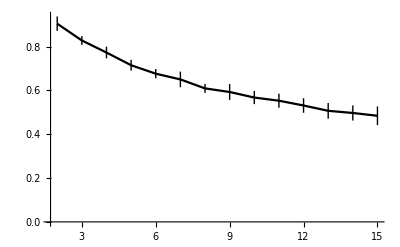

```mathematica
ListLinePlot[%47,PlotRange->All,PlotStyle->Black]
```

```mathematica
4
```

```mathematica
ListPlot[%27]
```

```mathematica
Clear[inp,ca]
```

```mathematica
inp[w_]:=inp[w]=Table[Table[CA[w,0.0001,1,0,1,10,4,1,y,x],{x,Range[1,30,2]}],{y,Range[2,30,2]}]
```

```mathematica
ca[w_]:=Monitor[Table[Mean[ParallelTable[Table[Table[CA[w,0.0001,1,0,1,10,z,num,y,x],{x,Range[1,30,2]}],{y,Range[2,30,2]}],{num,100}]],{z,10}],z]
```